```mathematica
dataC222=Flatten[Import["/Users/antonishadjipittas/Desktop/moldenscript/c_222_1.1.molden.xlsx"],1];

dataH1=Flatten[Import["/Users/antonishadjipittas/Desktop/moldenscript/h_1_1.1.molden.xlsx"],1];
(*import excel file with rows of all the primitive gaussians, note that the script outputs as a csv, so you need to open this csv with excel and save as excel format*)

dataCH4o1=Flatten[Import["/Users/antonishadjipittas/Desktop/moldenscript/ch4_22222_1.1.molden.xlsx"],1];

dataCH4o2=Flatten[Import["/Users/antonishadjipittas/Desktop/moldenscript/ch4_22222_2.1.molden.xlsx"],1];

Dimensions[dataC222]
Dimensions[dataH1]
Dimensions[dataCH4o1]
Dimensions[dataCH4o2]
```

{107,9}

{27,9}

{215,9}

{215,9}

```mathematica
Ν[i,j,k,α]=(2*α/Pi)^(3/4)*Sqrt[(8*α)^(i+j+k)*i!*j!*k!/((2*i)!*(2*j)!*(2*k)!)];(*Normalization constant N*)

gaus[x_,y_,z_,xn_,yn_,zn_,i_,j_,k_,α_]=Ν[i,j,k,α]*(x-xn)^i*(y-yn)^j*(z-zn)^k*Exp[-α*((x-xn)^2+(y-yn)^2+(z-zn)^2)];(*Gaussian orbital in cartesian coordinates*)

ϕH1[x_,y_,z_]= Sum[dataH1[[j]][[9]]*dataH1[[j]][[5]]*gaus[x,y,z,dataH1[[j]][[6]],dataH1[[j]][[7]],dataH1[[j]][[8]],IntegerPart[dataH1[[j]][[1]]],IntegerPart[dataH1[[j]][[2]]],IntegerPart[dataH1[[j]][[3]]],dataH1[[j]][[4]]],{j,1,27}];

ϕC222[x_,y_,z_]= Sum[dataC222[[j]][[9]]*dataC222[[j]][[5]]*gaus[x,y,z,dataC222[[j]][[6]],dataC222[[j]][[7]],dataC222[[j]][[8]],IntegerPart[dataC222[[j]][[1]]],IntegerPart[dataC222[[j]][[2]]],IntegerPart[dataC222[[j]][[3]]],dataC222[[j]][[4]]],{j,1,107}];
(*contructs the wavefunction, multiply the weight and corresponding contraction coefficient for that primitive, and then multiply by the primitive gaussian function*)

ϕCH4o1[x_,y_,z_]= Sum[dataCH4o1[[j]][[9]]*dataCH4o1[[j]][[5]]*gaus[x,y,z,dataCH4o1[[j]][[6]],dataCH4o1[[j]][[7]],dataCH4o1[[j]][[8]],IntegerPart[dataCH4o1[[j]][[1]]],IntegerPart[dataCH4o1[[j]][[2]]],IntegerPart[dataCH4o1[[j]][[3]]],dataCH4o1[[j]][[4]]],{j,1,215}];
(*contructs the wavefunction, multiply the weight and corresponding contraction coefficient for that primitive, and then multiply by the primitive gaussian function*)

ϕCH4o2[x_,y_,z_]= Sum[dataCH4o2[[j]][[9]]*dataCH4o2[[j]][[5]]*gaus[x,y,z,dataCH4o2[[j]][[6]],dataCH4o2[[j]][[7]],dataCH4o2[[j]][[8]],IntegerPart[dataCH4o2[[j]][[1]]],IntegerPart[dataCH4o2[[j]][[2]]],IntegerPart[dataCH4o2[[j]][[3]]],dataCH4o2[[j]][[4]]],{j,1,215}];
(*contructs the wavefunction, multiply the weight and corresponding contraction coefficient for that primitive, and then multiply by the primitive gaussian function*)
```

```mathematica
Re[NIntegrate[ϕH1[x,y,z]^2,{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*test normalization of H*)

Re[NIntegrate[(ϕC222[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*test normalization of C*)

Re[NIntegrate[(ϕCH4o1[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*test normalization of C*)

Re[NIntegrate[(ϕCH4o2[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*test normalization of C*)
```

1.00002

1.

1.

0.999999

```mathematica
Re[NIntegrate[ϕH1[x,y,z]ϕC222[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]

Re[NIntegrate[ϕCH4o2[x,y,z]ϕC222[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]

Re[NIntegrate[ϕCH4o1[x,y,z]ϕH1[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*Check overlap between two wavefunctions*)

Re[NIntegrate[ϕCH4o2[x,y,z]ϕCH4o1[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Method->{"LocalAdaptive",Method->"MultiDimensionalRule"}]]
(*Check overlap between two wavefunctions*)
```

0.37503

-0.00252369

0.377356

-1.12908×10^-7

General::munfl: Exp[-65891.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9880.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2246.52] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

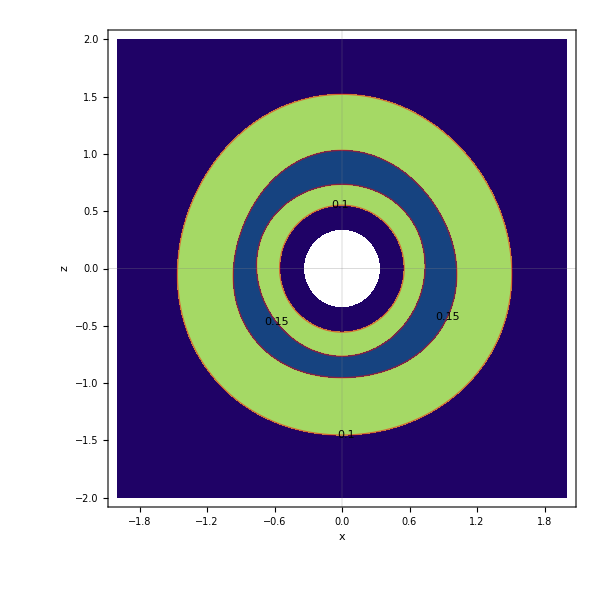
ShowLegend[-Graphics-]

```mathematica
(*Contour Plot*)
ShowLegend[ContourPlot[ϕCH4o2[x,0,z],{x,-2, 2},{z,-2,2},Contours->{0.35,0.3,0.25,0.2,0.15,0.1},ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),ContourShading->True,ColorFunction->"BlueGreenYellow",ImageSize->600,ContourStyle->{{Red,Thick}},PlotPoints->100,GridLines->{{0},{0}},FrameLabel->{"x","z"},FrameStyle->Directive[15]]]
```

General::munfl: Exp[-8236.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1235.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8234.35] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

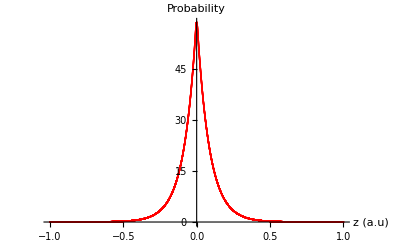

```mathematica
(*1D plot - Prob density along Z axis*)
pV5Zzplot=Table[{z,Abs[ϕC222[0,0,z]]^2},{z,-1,1,0.0001}];
abc=ListPlot[pV5Zzplot,PlotStyle->{Red},AxesLabel->{"z (a.u)","Probability"}];
Show[abc,PlotRange->All]
```